### 2次曲線（方程式）の定義

```mathematica
F[x_,y_]=2x^2+4*x*y-y^2+x-2y-1
```

-1+x+2 x^2-2 y+4 x y-y^2

```mathematica
F[x,y]
```

-1+x+2 x^2-2 y+4 x y-y^2

### 2次曲線の描画

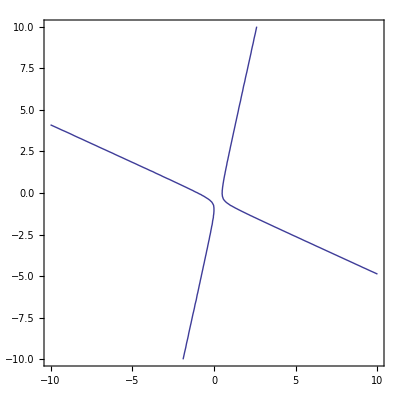

```mathematica
ContourPlot[F[x,y]==0,{x,-10,10},{y,-10,10}]
```

### 原点の平行移動

```mathematica
F[x+a,y+b]
```

-1+a+x+2 (a+x)^2-2 (b+y)+4 (a+x) (b+y)-(b+y)^2

### F[x + a, y + b] のxの係数

```mathematica
D[F[x+a,y+b],x]/.x->0/.y->0
```

1+4 a+4 b

### F[x + a, y + b] のyの係数

```mathematica
D[F[x+a,y+b],y]/.x->0/.y->0
```

-2+4 a-2 b

### F[x + a, y + b] の1次の項が消えるためには…

```mathematica
Solve[{1+4 a+4 b==0,-2+4 a-2 b==0},{a,b}]
```

{{a→1/4,b→-1/2}}

```mathematica
Expand[F[x+1/4,y-1/2]]
```

-3/8+2 x^2+4 x y-y^2

### 座標の直交変換により，2次の項を簡略化する

```mathematica
A={{2,2},{2,-1}}
```

{{2,2},{2,-1}}

```mathematica
Expand[{x,y}.A.{x,y}]
```

2 x^2+4 x y-y^2

```mathematica
Eigensystem[A]
```

{{3,-2},{{2,1},{-1,2}}}

```mathematica
P={{2/Sqrt[5],-1/Sqrt[5]},{1/Sqrt[5],2/Sqrt[5]}}
```

{{2/(√5),-1/(√5)},{1/(√5),2/(√5)}}

```mathematica
P//MatrixForm
```

(2/(√5) | -1/(√5)
1/(√5) | 2/(√5))

```mathematica
Transpose[P].A.P
```

{{3,0},{0,-2}}

```mathematica
P.{x,y}
```

{(2 x)/(√5)-y/(√5),x/(√5)+(2 y)/(√5)}

```mathematica
Expand[F[(2 x)/(√5)-y/(√5)+1/4,x/(√5)+(2 y)/(√5)-1/2]]
```

-3/8+3 x^2-2 y^2